## Pre

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
?dispersion`*
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Needs["PolygonPlotMarkers`"]
```

```mathematica
(1+g[#])&/@{a,b,c}
```

{1+g[a],1+g[b],1+g[c]}

```mathematica
shapes=PolygonMarker[All];
shapesTip=Table[
Tooltip[Graphics[{FaceForm[pltcolors[[i]]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[shapes[[i]],Scaled[.3]]},ImageSize->15],shapes[[i]]],
{i,1,Length@pltcolors}]
shapesTipTable={shapesTip,
Table[i,{i,1,Length@pltcolors}]}//Transpose
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{-Graphics-,1},{-Graphics-,2},{-Graphics-,3},{-Graphics-,4},{-Graphics-,5},{-Graphics-,6},{-Graphics-,7},{-Graphics-,8},{-Graphics-,9},{-Graphics-,10},{-Graphics-,11},{-Graphics-,12},{-Graphics-,13},{-Graphics-,14},{-Graphics-,15}}

```mathematica
pltmarkers={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Discrete Beams for Comparison

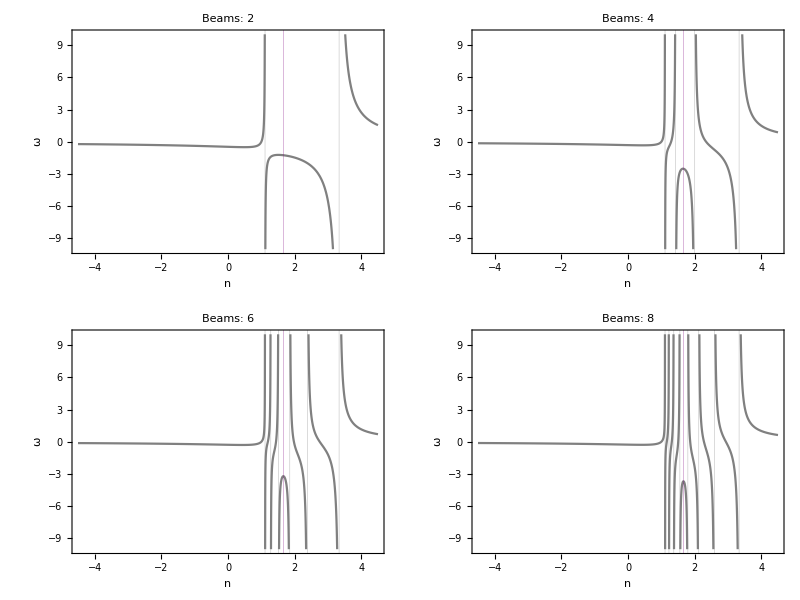

```mathematica
{{NBeamsOmegaNPlt[NBeamsLR[2]],
NBeamsOmegaNPlt[NBeamsLR[4]]},
{NBeamsOmegaNPlt[NBeamsLR[6]],
NBeamsOmegaNPlt[NBeamsLR[8]]}}//Grid
```

```mathematica
{{NBeamsOmegaKPlt[NBeamsLR[2]][[2]],
NBeamsOmegaKPlt[NBeamsLR[4]][[2]]},
{NBeamsOmegaKPlt[NBeamsLR[6]][[2]],
NBeamsOmegaKPlt[NBeamsLR[8]][[2]]}}//Grid
```

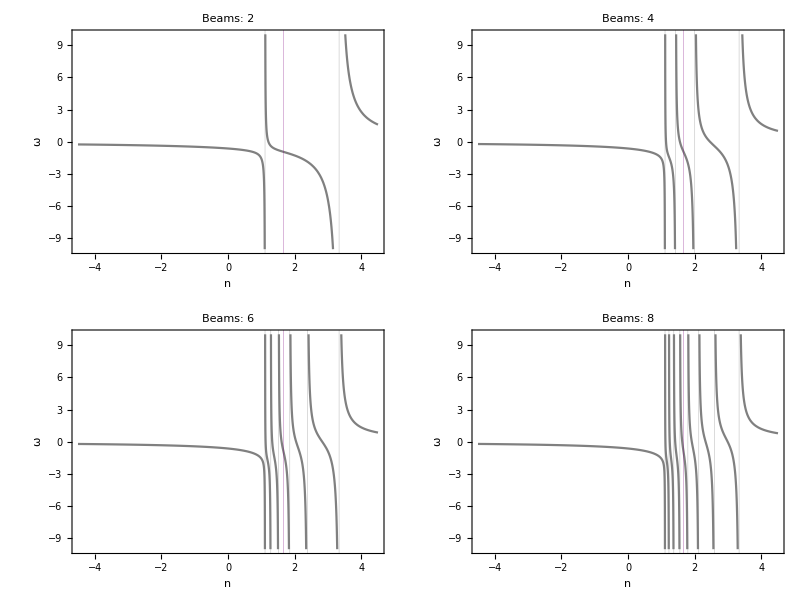

```mathematica
{{NBeamsOmegaNPlt[NBeamsH[2]],
NBeamsOmegaNPlt[NBeamsH[4]]},
{NBeamsOmegaNPlt[NBeamsH[6]],
NBeamsOmegaNPlt[NBeamsH[8]]}}//Grid
```

```mathematica
{{NBeamsOmegaKPlt[NBeamsH[2]][[2]],
NBeamsOmegaKPlt[NBeamsH[4]][[2]]},
{NBeamsOmegaKPlt[NBeamsH[6]][[2]],
NBeamsOmegaKPlt[NBeamsH[8]][[2]]}}//Grid
```

## Continuous

```mathematica
Assuming[omega∈Reals&&k∈Reals&&ct∈Reals&&ct1∈Reals&&ct2∈Reals,
Integrate[ ( 1/(1-k ct/omega) ),{ct,ct2,ct1}]
]
```

ConditionalExpression[(omega (-Log[1-(ct1 k)/omega]+Log[1-(ct2 k)/omega]))/k,ct2>0&&ct1>ct2&&((omega<0&&(k≤omega/ct2||k≥omega/ct1))||omega==0||(omega>0&&(k≤omega/ct1||k≥omega/ct2)))]

```mathematica
Assuming[omega∈Reals&&k∈Reals&&ct∈Reals&&ct1∈Reals&&ct2∈Reals,
Integrate[ ( ct/(1-k ct/omega) ),{ct,ct2,ct1}]
]
```

ConditionalExpression[(omega ((-ct1+ct2) k+omega Log[(ct2 k-omega)/(ct1 k-omega)]))/k^2,ct2<ct1&&((k<0&&omega<ct1 k&&omega≤ct2 k)||(k>0&&omega<ct2 k))]

```mathematica
Assuming[omega∈Reals&&k∈Reals&&ct∈Reals&&ct1∈Reals&&ct2∈Reals,
Integrate[ ( ct^2/(1-k ct/omega) ),{ct,ct2,ct1}]
]
```

ConditionalExpression[(omega (-(ct1-ct2) k ((ct1+ct2) k+2 omega)+2 omega^2 Log[(ct2 k-omega)/(ct1 k-omega)]))/(2 k^3),ct2<ct1&&((k<0&&omega<ct1 k&&omega≤ct2 k)||(k>0&&omega<ct2 k))]

I can rewrite the EoM

```mathematica
eqnCont1[c1_,c2_]:=(-4n^3+(c2-c1)(1+(c1+c2)n/2))==(n^2-1)Log[(n-c2)/(n-c1)]
```

```mathematica
eqnCont1[0.3,0.9]
```

0.6 (1+0.6 n)-4 n^3==(-1+n^2) Log[(-0.9+n)/(-0.3+n)]

```mathematica
FindRoot[eqnCont1[0.3,0.9],{n,-0.3}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{n→-0.349559}

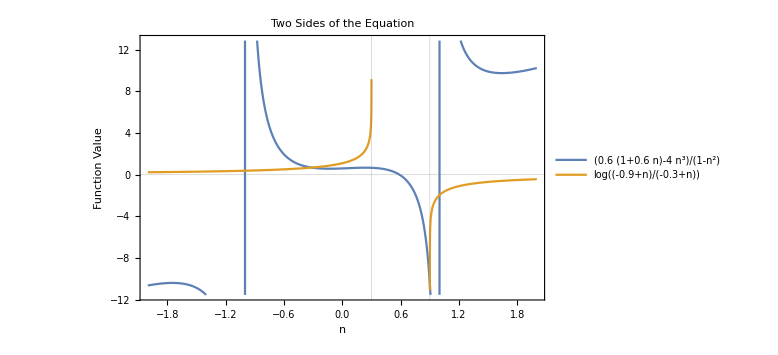

```mathematica
Plot[{(0.6000000000000001 (1+0.6 n)-4 n^3)/(1-n^2),Log[(-0.9+n)/(-0.3+n)]},{n,-2,2},Frame->True,ImageSize->Large,Axes->False,GridLines->{{0.3,0.9}, {0}},PlotLegends->Placed["Expressions",{Right,Bottom}],PlotLabel->"Two Sides of the Equation",FrameLabel->{"n","Function Value"}]
```

```mathematica
NSolve[
eqnCont1[0.3,0.9]/.n->(k/omega),
omega]
```

NSolve[0.6 (0.6+k/omega)-(4 omega)/k==(1-k^2/omega^2) Log[(-0.9+k/omega)/(-0.3+k/omega)],omega]

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

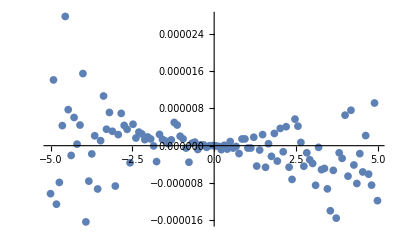

```mathematica
ListPlot[Table[
{k,omega/.FindRoot[eqnCont1[0.3,0.9]/.n->(k/omega),{omega,k}]},
{k,-5,5,0.09}],PlotRange->Full
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

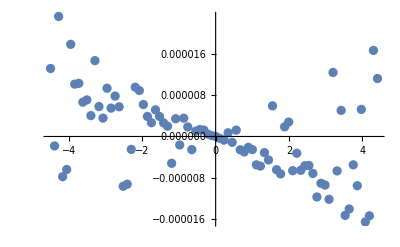

```mathematica
ListPlot@Table[
{k,omega/.FindRoot[0.6000000000000001 (0.6+k/omega)-(4 omega)/k==(1-k^2/omega^2) Log[(-0.9+k/omega)/(-0.3+k/omega)],{omega,0.3k}]},
{k,-4.5,4.5,0.11}]
```

```mathematica
intFun0[omega_,k_,ct1_,ct2_]:=(omega (-Log[Abs[1-(ct1 k)/omega]]+Log[Abs[1-(ct2 k)/omega]]))/k;
intFun1[omega_,k_,ct1_,ct2_]:=(omega ((-ct1+ct2) k+omega Log[Abs[(ct2 k-omega)/(ct1 k-omega)]]))/k^2;
intFun2[omega_,k_,ct1_,ct2_]:=(omega (-(ct1-ct2) k ((ct1+ct2) k+2 omega)+2 omega^2 Log[Abs[(ct2 k-omega)/(ct1 k-omega)]]))/(2 k^3);
intFun0n[n_,ct1_,ct2_]:=(-Log[Abs[1-ct1 n]]+Log[Abs[1-ct2 n]])/n;
intFun1n[n_,ct1_,ct2_]:=((-ct1+ct2) +Log[Abs[(ct2 n-1)/(ct1 n-1)]]/n)/n;
intFun2n[n_,ct1_,ct2_]:=(-(ct1-ct2) ((ct1+ct2) +2/n)+2 Log[Abs[(ct2 n-1)/(ct1 n-1)]]/n^2)/(2  n);
```

```mathematica
i0Homza1=intFun0n[n,0.9,0.3]
i2Homza1=intFun2n[n,0.9,0.3]//FullSimplify
i1Homza1=intFun1n[n,0.9,0.3]//FullSimplify


i0Homza1abs=intFun0n[n,c1,c2]
i2Homza1abs=intFun2n[n,c1,c2]//FullSimplify
i1Homza1abs=intFun1n[n,c1,c2]//FullSimplify

omegaFunHoMZA1[n_]:=(-4(i0Homza1)(i2Homza1)+4 i1Homza1^2+8(i0Homza1+i2Homza1))/(-16)

omegaFunHoMAA1[n_]:=(intFun0n[n,0.9,0.3]-intFun2n[n,0.9,0.3])/(4)
```

(-Log[Abs[1-0.9 n]]+Log[Abs[1-0.3 n]])/n

((-0.6-0.36 n) n+1. Log[Abs[0.333333+0.740741/(1.11111-1. n)]])/n^3

(-0.6 n+1. Log[Abs[0.333333-0.740741/(-1.11111+1. n)]])/n^2

(-Log[Abs[1-c1 n]]+Log[Abs[1-c2 n]])/n

(-(c1-c2) n (2+(c1+c2) n)+2 Log[Abs[(-1+c2 n)/(-1+c1 n)]])/(2 n^3)

((-c1+c2) n+Log[Abs[(-1+c2 n)/(-1+c1 n)]])/n^2

We can find the limits

```mathematica
Limit[
{omegaFunHoMAA1[n] n,omegaFunHoMAA1[n]},
n->1/0.3]
```

{-∞,-∞}

```mathematica
Limit[
{omegaFunHoMAA1[n] n,omegaFunHoMAA1[n]},
n->Infinity]
Limit[
{omegaFunHoMZA1[n] n,omegaFunHoMZA1[n]},
n->Infinity]
```

{-0.184653,0.}

{0.729306,0.}

These limits can be calcualted without going into examples

```mathematica
Limit[{n ,1}((intFun0n[n,c1,c2]-intFun2n[n,c1,c2])/4),n->Infinity]//FullSimplify
```

{1/8 (c1^2-c2^2-2 Log[-c1]+2 Log[-c2]),0}

```mathematica
Limit[{n ,1}( (-4(i0Homza1abs)(i2Homza1abs)+4 i1Homza1abs^2+8(i0Homza1abs+i2Homza1abs))/(-16) ),n->Infinity]//FullSimplify
```

{1/4 (c1^2-c2^2+2 Log[-c1]-2 Log[-c2]),0}

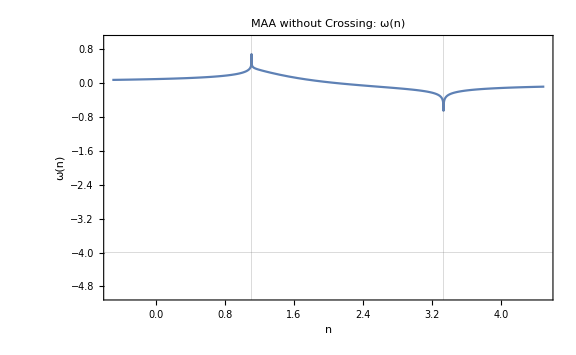

```mathematica
Plot[omegaFunHoMAA1[n],{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{1/0.3,1/0.9}, {-4}},PlotRange->{Automatic,{-5,1}},PlotLabel->"MAA without Crossing: ω(n)",FrameLabel->{"n","ω(n)"}]
```

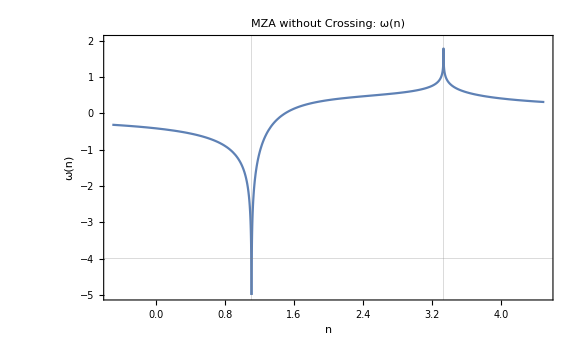

```mathematica
Plot[omegaFunHoMZA1[n],{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{1/0.3,1/0.9}, {-4}},PlotRange->{Automatic,{-5,2}},PlotLabel->"MZA without Crossing: ω(n)",FrameLabel->{"n","ω(n)"}]
```

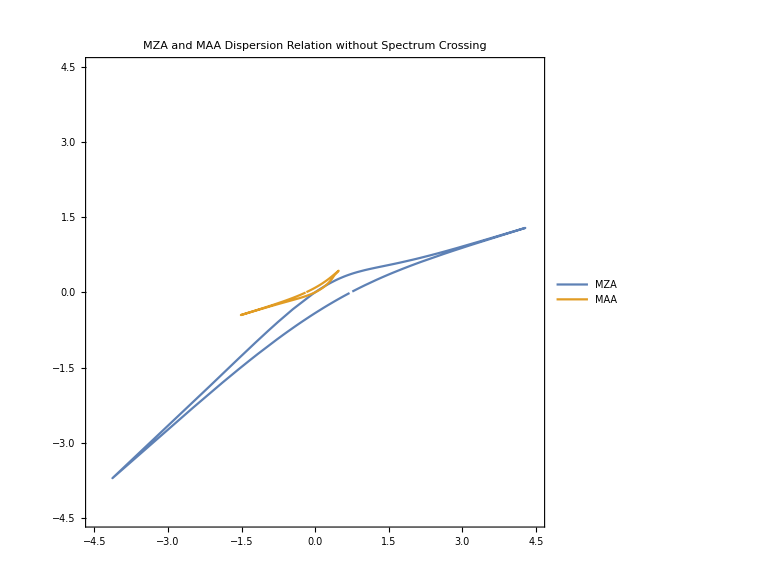

```mathematica
ParametricPlot[
{
{n omegaFunHoMZA1[n],omegaFunHoMZA1[n]},
{n omegaFunHoMAA1[n],omegaFunHoMAA1[n]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-4.5,4.5},{-4.5,4.5}},PlotLegends->Placed[{"MZA","MAA"},{Left,Top}],PlotLabel->"MZA and MAA Dispersion Relation without Spectrum Crossing"]
```

Nonhomogeneous Emission

```mathematica
omegaFunMAA1[n_]:=(intFun0n[n,0.9,(0.9+0.3)/2]-intFun0n[n,(0.9+0.3)/2,0.3]-(intFun2n[n,0.9,(0.9+0.3)/2]-intFun2n[n,(0.9+0.3)/2,0.3]))/(4)
```

```mathematica
i0i2[omega_,k_,ct1_,ct2_,g_]:=g ( (1/n-1/n^3)Log[(1-n ct2)/(1-n ct1)] - (ct2-ct1)((ct1+ct2)/2+1/n)/n )
lnArgument[ct1_,ct2_,ct0_]:=Abs[(1-n ct0)^2/((1-n ct1)(1-n ct2))]
```

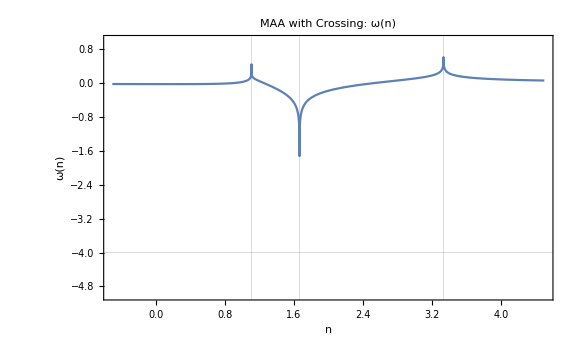

```mathematica
Plot[omegaFunMAA1[n],{n,-0.5,4.5},Frame->True,ImageSize->Large,GridLines->{{1/0.3,1/0.6,1/0.9}, {-4}},PlotRange->{Automatic,{-5,1}},PlotLabel->"MAA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"}]
```

```mathematica
1/0.3
1/0.9
```

3.33333

1.11111

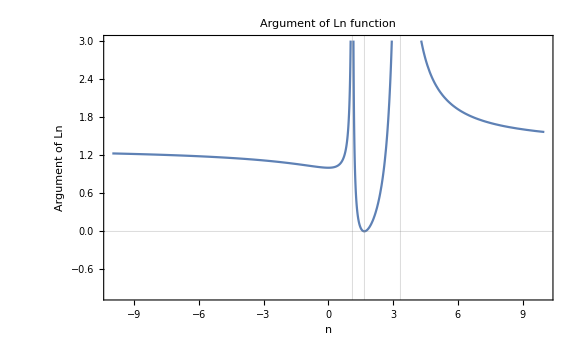

```mathematica
Plot[lnArgument[0.9,0.3,0.6],{n,-10,10},Frame->True,ImageSize->Large,GridLines->{{1/0.3,1/0.6,1/0.9}, {0}},PlotRange->{Automatic,{-1,3}},PlotLabel->"Argument of Ln function",FrameLabel->{"n","Argument of Ln"}]
```

```mathematica
Limit[{n omegaFunMAA1[n],omegaFunMAA1[n]},n->Infinity]
Limit[{n omegaFunMZA[n],omegaFunMZA[n]},n->Infinity]
Limit[{n omegaFunMAA1[n],omegaFunMAA1[n]},n->1/0.3]
```

{0.0944205,0.}

{-0.098841,0.}

{∞,∞}

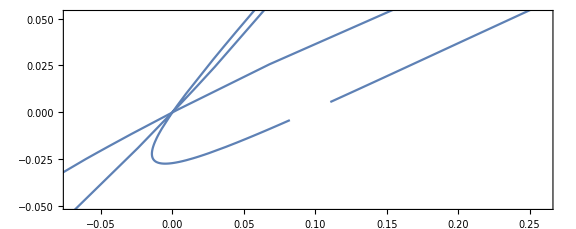

```mathematica
ParametricPlot[
{n omegaFunMAA1[n],omegaFunMAA1[n]},
{n,-20,20},Frame->True,ImageSize->Large]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

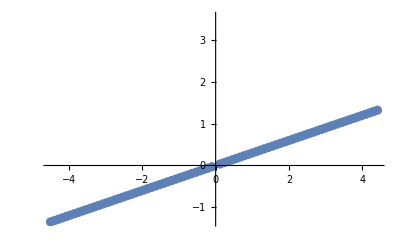

```mathematica
ListPlot@Table[
{k,omega/.FindRoot[-4==intFun0[omega,k,0.9,(0.9+0.3)/2]+intFun0[omega,k,(0.9+0.3)/2,0.3]-(intFun2[omega,k,0.9,(0.9+0.3)/2]+intFun2[omega,k,(0.9+0.3)/2,0.3]),
{omega,0.1}]},
{k,-4.5,4.5,0.11}]
```

## Direct Approach 1

```mathematica
ContiIntsOriginal[i_,omega_,k_]:=Assuming[omega∈Reals&&k∈Reals,
Integrate[-Sin[theta]((2Pi)/(ArcCos@0.3-ArcCos@0.9)) ( Cos[theta]^i/(1-omega Cos[theta]/k) ),{theta,ArcCos@0.9,ArcCos@0.3}]
];
ContiInts[i_,omega_,k_,theta1_,theta2_]:=(2 k (omega/k)^-i π (Beta[(omega Cos[theta1])/k,1+i,0]-Beta[(omega Cos[theta2])/k,1+i,0]))/(omega (theta1-theta2));
```

```mathematica
ContiInts[0,omega,k,ArcCos@0.9,ArcCos@0.3]
```

-(7.7087 k (-Log[1-(0.9 omega)/k]+Log[1-(0.3 omega)/k]))/omega

```mathematica
ContiAxialSymEqn[omega_,k_,theta1_,theta2_]:=4omega==ContiInts[0,omega,k,theta1,theta2]-ContiInts[2,omega,k,theta1,theta2]
```

```mathematica
ContiAxialSymEqn[omega,0.4,ArcCos@0.9,ArcCos@0.3]//Simplify
```

4 omega==(0.493357 (-Beta[0.75 omega,3,0]+Beta[2.25 omega,3,0]))/omega^3-(3.08348 (-Log[1-2.25 omega]+Log[1-0.75 omega]))/omega

```mathematica
NSolve[ContiAxialSymEqn[omega,0.4,ArcCos@0.9,ArcCos@0.3],omega]
```

NSolve[4 omega==(0.493357 (-Beta[0.75 omega,3,0]+Beta[2.25 omega,3,0]))/omega^3-(3.08348 (-Log[1-2.25 omega]+Log[1-0.75 omega]))/omega,omega]

```mathematica
Table[
omega/.FindRoot[ContiAxialSymEqn[omega,0.4,ArcCos@0.9,ArcCos@0.3],{omega,rootinit}],
{rootinit,-5,5,0.09}]
```

{-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457,-0.445457-1.69337×10^-16 ⅈ,-0.445457+1.61998×10^-16 ⅈ,1.42768-2.98483×10^-17 ⅈ,1.42768-6.88169×10^-17 ⅈ,1.42768+4.5912×10^-16 ⅈ,1.42768-2.4941×10^-17 ⅈ,1.42768+4.66029×10^-17 ⅈ,1.42768+1.37876×10^-15 ⅈ,1.42768-5.07148×10^-17 ⅈ,1.42768+6.70095×10^-17 ⅈ,1.42768-7.76134×10^-17 ⅈ,1.42768-8.93384×10^-17 ⅈ,1.42768-8.20334×10^-17 ⅈ,1.42768-8.36572×10^-17 ⅈ,1.42768-8.03436×10^-17 ⅈ,1.42768-1.03441×10^-16 ⅈ,1.42768-9.54473×10^-17 ⅈ,1.42768-8.34038×10^-17 ⅈ,1.42768-7.46888×10^-17 ⅈ,1.42768-9.97187×10^-17 ⅈ,1.42768-1.02503×10^-16 ⅈ,1.42768-8.28439×10^-17 ⅈ,1.42768-5.24147×10^-17 ⅈ,1.42768-9.50352×10^-17 ⅈ,1.42768-9.01846×10^-17 ⅈ,1.42768-9.58721×10^-17 ⅈ,1.42768-5.22652×10^-17 ⅈ,1.42768-1.11491×10^-16 ⅈ,1.42768-8.82574×10^-17 ⅈ,1.42768-9.07785×10^-17 ⅈ,1.42768-9.62105×10^-17 ⅈ,1.42768-7.26903×10^-17 ⅈ,1.42768-7.84539×10^-17 ⅈ,1.42768-6.9992×10^-17 ⅈ,-0.445457-2.84235×10^-16 ⅈ,1.42768-8.80566×10^-17 ⅈ,-0.445457-2.65928×10^-17 ⅈ,-0.445457-3.13044×10^-17 ⅈ,-0.445457-2.75786×10^-17 ⅈ,-0.445457-2.98863×10^-17 ⅈ,-0.445457-2.65292×10^-17 ⅈ,-0.445457-2.70612×10^-17 ⅈ,-0.445457-2.34447×10^-17 ⅈ,-0.445457-2.5862×10^-17 ⅈ,-0.445457-2.73537×10^-17 ⅈ,-0.445457-2.35693×10^-17 ⅈ,-0.445457-2.65066×10^-17 ⅈ,-0.445457-2.70705×10^-17 ⅈ,-0.445457-2.27763×10^-17 ⅈ,-0.445457-2.06798×10^-17 ⅈ,-0.445457-2.30209×10^-17 ⅈ}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

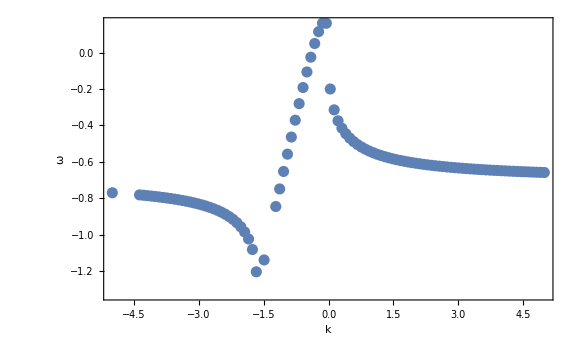

```mathematica
ListPlot[
Table[
{k,omega/.FindRoot[ContiAxialSymEqn[omega,k,ArcCos@0.9,ArcCos@0.3],{omega,-5}]},
{k,-5,5,0.09}],
Frame->True,FrameLabel->{"k","ω"},ImageSize->Large]
```

```mathematica
N@{2441,1293}/1939023
N@{29+7,23+10}/15812
```

{0.00125888,0.000666831}

{0.00227675,0.00208702}

$Aborted

## MZA and Bimodal (non homogeneous)

```mathematica
intFun0[1,n,0.9,(0.9+0.3)/2]-intFun0[1,n,(0.9+0.3)/2,0.3]
intFun2[1,n,0.9,(0.9+0.3)/2]-intFun2[1,n,(0.9+0.3)/2,0.3]//FullSimplify
intFun1[1,n,0.9,(0.9+0.3)/2]-intFun1[1,n,(0.9+0.3)/2,0.3]//FullSimplify

i0mza=intFun0n[n,0.9,(0.9+0.3)/2]-intFun0n[n,(0.9+0.3)/2,0.3]
i2mza=intFun2n[n,0.9,(0.9+0.3)/2]-intFun2n[n,(0.9+0.3)/2,0.3]//FullSimplify
i1mza=intFun1n[n,0.9,(0.9+0.3)/2]-intFun1n[n,(0.9+0.3)/2,0.3]//FullSimplify

i0mzaabs=g1 intFun0n[n,c1,c0]+g2 intFun0n[n,c0,c2]
i2mzaabs=g1 intFun2n[n,c1,c0]+g2 intFun2n[n,c0,c2]//FullSimplify
i1mzaabs=g1 intFun1n[n,c1,c0]+g2 intFun1n[n,c0,c2]//FullSimplify


omegaFunMZA[n_]:=(-4(i0mza)(i2mza)+4 i1mza^2+8(i0mza+i2mza))/(-16)


omegaFunMAA1abs[n_]:=(g1 intFun0n[n,c1,c0]+g2 intFun0n[n,c0,c2]-(g1 intFun2n[n,c1,c0]+g2  intFun2n[n,c0,c2]))/(4)
omegaFunMZA1abs[n_]:=(-4(i0mzaabs)(i2mzaabs)+4 i1mzaabs^2+8(i0mzaabs+i2mzaabs))/(-16)
```

(-Log[Abs[1-0.9 n]]+Log[Abs[1-0.6 n]])/n-(-Log[Abs[1-0.6 n]]+Log[Abs[1-0.3 n]])/n

((-5.55112×10^-17-0.09 n) n-1. Log[Abs[0.5+0.833333/(1.66667-1. n)]]+1. Log[Abs[0.666667-0.37037/(-1.11111+1. n)]])/n^3

(-5.55112×10^-17 n+Log[Abs[0.666667+0.37037/(1.11111-1. n)]]-1. Log[Abs[0.5-0.833333/(-1.66667+1. n)]])/n^2

(-Log[Abs[1-0.9 n]]+Log[Abs[1-0.6 n]])/n-(-Log[Abs[1-0.6 n]]+Log[Abs[1-0.3 n]])/n

((-5.55112×10^-17-0.09 n) n-1. Log[Abs[0.5+0.833333/(1.66667-1. n)]]+1. Log[Abs[0.666667-0.37037/(-1.11111+1. n)]])/n^3

(-5.55112×10^-17 n+Log[Abs[0.666667+0.37037/(1.11111-1. n)]]-1. Log[Abs[0.5-0.833333/(-1.66667+1. n)]])/n^2

(g1 (Log[Abs[1-c0 n]]-Log[Abs[1-c1 n]]))/n+(g2 (-Log[Abs[1-c0 n]]+Log[Abs[1-c2 n]]))/n

(n (-2 c1 g1+2 c0 (g1-g2)-c1^2 g1 n+c0^2 (g1-g2) n+c2 g2 (2+c2 n))+2 g1 Log[Abs[(-1+c0 n)/(-1+c1 n)]]+2 g2 Log[Abs[(-1+c2 n)/(-1+c0 n)]])/(2 n^3)

((c0 g1-c1 g1-c0 g2+c2 g2) n+g1 Log[Abs[(-1+c0 n)/(-1+c1 n)]]+g2 Log[Abs[(-1+c2 n)/(-1+c0 n)]])/n^2

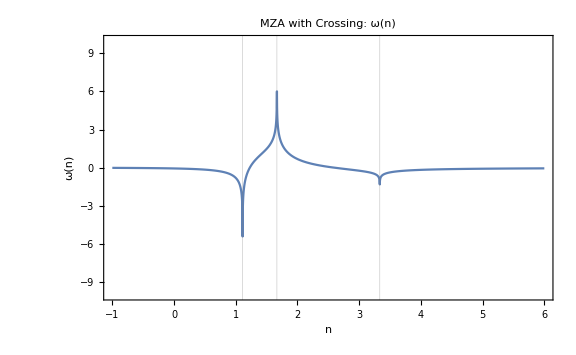

```mathematica
Plot[omegaFunMZA[n],{n,-1,6},Frame->True,ImageSize->Large,PlotRange->{Automatic,{-10,10}},GridLines->{{1/0.3,1/0.6,1/0.9}, None},PlotLabel->"MZA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"}]
```

Are MZA and MAA some kind of mirror of omega=0?

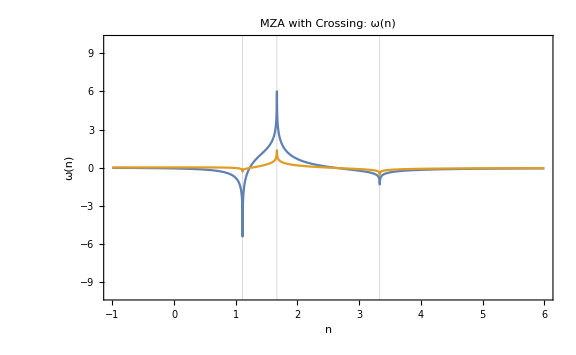

```mathematica
Plot[{omegaFunMZA[n],-omegaFunMAA1[n]},{n,-1,6},Frame->True,ImageSize->Large,PlotRange->{Automatic,{-10,10}},GridLines->{{1/0.3,1/0.6,1/0.9}, None},PlotLabel->"MZA with Crossing: ω(n)",FrameLabel->{"n","ω(n)"}]
```

At the limit n->Infinity, we have the omega-k becomes a point:

```mathematica
Limit[{n omegaFunMZA[n],omegaFunMZA[n]},n->Infinity]

Limit[{n omegaFunMAA1[n],omegaFunMZA[n]},n->Infinity]
```

{-0.098841,0.}

{0.0944205,0.}

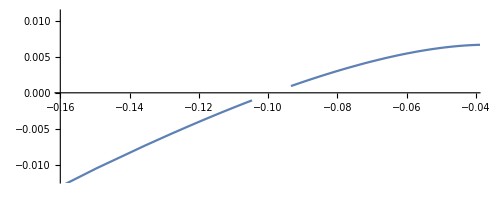

```mathematica
ParametricPlot[{n omegaFunMZA[n],omegaFunMZA[n]},
{n,-100,100},GridLines->{{-1,0,1}, {-1,0,1}}]
```

The singularities determines the asymptotic behavior. For n->1/0.3 or n->1/0.9, the omega values can change a lot under a tiny change of n, as also k. So the relative between omega and k becomes linear near these singularities.

Now combine MZA and MAA

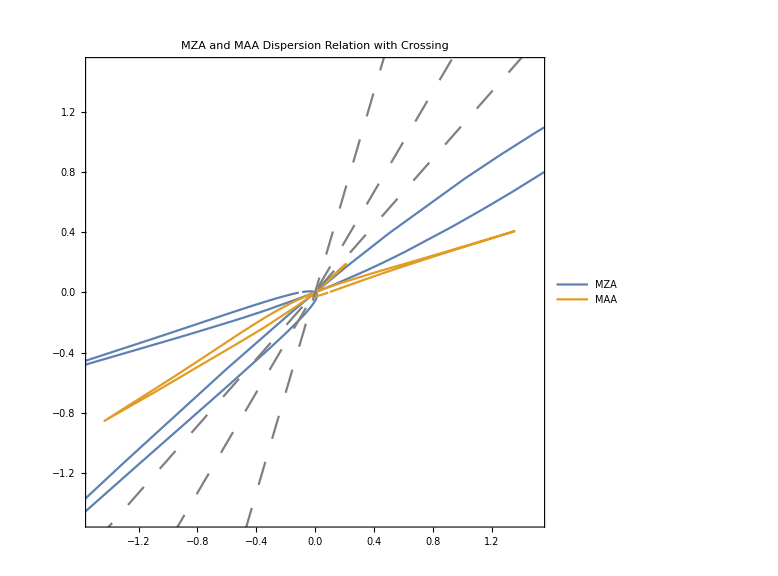

```mathematica
Show[
ParametricPlot[
{
{n omegaFunMZA[n],omegaFunMZA[n]},
{n omegaFunMAA1[n],omegaFunMAA1[n]}
},
{n,-50,50},Frame->True,ImageSize->Large,PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotLegends->Placed[{"MZA","MAA"},{Right,Top}],PlotLabel->"MZA and MAA Dispersion Relation with Crossing"],
Plot[{1/0.9x,1/0.6x,1/0.3x},{x,-4.5,4.5},PlotStyle->Directive[Gray,Dashing[0.03]]]
]
```

Not really good beacause the sampling around singularities are not large enough.

```mathematica
paraDataMZA1=Sort[
Join[
Table[{n omegaFunMZA[n],omegaFunMZA[n]},{n,-10,10,0.09}],
Table[{n omegaFunMZA[n],omegaFunMZA[n]},{n,1/0.3+0.0001,1/0.3+0.1,0.00009}],
Table[{n omegaFunMZA[n],omegaFunMZA[n]},{n,1/0.9+0.0001,1/0.9+0.1,0.00009}]
],
#1[[1]]<#2[[1]]&]//Quiet
paraDataMAA1=Sort[
Join[
Table[{n omegaFunMAA1[n],omegaFunMAA1[n]},{n,-10,10,0.09}],
Table[{n omegaFunMAA1[n],omegaFunMAA1[n]},{n,1/0.3+0.0001,1/0.3+0.1,0.00009}],
Table[{n omegaFunMAA1[n],omegaFunMAA1[n]},{n,1/0.9+0.0001,1/0.9+0.1,0.00009}]
],
#1[[1]]<#2[[1]]&]//Quiet
```

{{-2.21284,-2.06807},{-1.31641,-1.34328},2442,{6.44651+0. ⅈ,1.93389+0. ⅈ}}
 |  |  |  |

{{0.648547-1.42146 ⅈ,0.583639-1.2792 ⅈ},2443,{-0.644517+0. ⅈ,-0.179531+0. ⅈ}}
 |  |  |  |

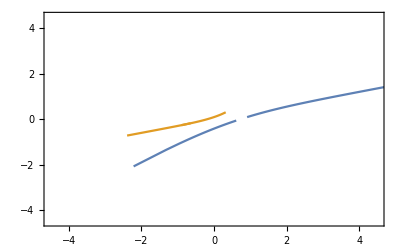

```mathematica
ListPlot[{paraDataMZA1,paraDataMAA1},PlotRange->{{-4.5,4.5},{-4.5,4.5}},Frame->True,Joined->True]
```

```mathematica
Limit[{n ,1}omegaFunMAA1abs[n],n->Infinity]//FullSimplify
Limit[{n ,1}omegaFunMZA1abs[n],n->Infinity]//FullSimplify
```

{1/8 (c1^2 g1-c2^2 g2+c0^2 (-g1+g2)+2 (g1-g2) Log[-c0]-2 g1 Log[-c1]+2 g2 Log[-c2]),0}

{1/4 (c1^2 g1-c2^2 g2+c0^2 (-g1+g2)+2 (-g1+g2) Log[-c0]+2 g1 Log[-c1]-2 g2 Log[-c2]),0}

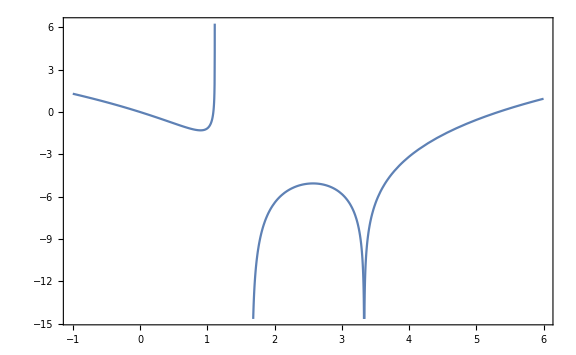

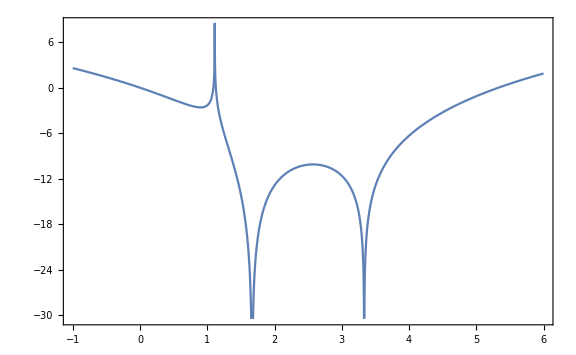

```mathematica
Plot[
Log[(1-n 0.6)^(g1-g2)/( (1-n 0.9)^g1 (1-n 0.3)^g2 )]/.{g1->1,g2->-2},
{n,-1,6},Frame->True,ImageSize->Large]
Plot[
Log[(1-n 0.6)^(g1-g2)/( (1-n 0.9)^g1 (1-n 0.3)^g2 )]/.{g1->2,g2->-4},
{n,-1,6},Frame->True,ImageSize->Large]
```

```mathematica
omegaFunMZAGeneral[1,0.9,0.3,0.6,1,1]
```

1/16 (-(4 ((c0 g1-c1 g1-c0 g2+c2 g2) n+g1 Log[(-1+c0 n)/(-1+c1 n)]+g2 Log[(-1+c2 n)/(-1+c0 n)])^2)/n^4+1/n^3 2 ((g1 (Log[1-c0 n]-Log[1-c1 n]))/n+(g2 (-Log[1-c0 n]+Log[1-c2 n]))/n) (n (-2 c1 g1+2 c0 (g1-g2)-c1^2 g1 n+c0^2 (g1-g2) n+c2 g2 (2+c2 n))+2 g1 Log[(-1+c0 n)/(-1+c1 n)]+2 g2 Log[(-1+c2 n)/(-1+c0 n)])-8 ((g1 (Log[1-c0 n]-Log[1-c1 n]))/n+(g2 (-Log[1-c0 n]+Log[1-c2 n]))/n+1/(2 n^3)(n (-2 c1 g1+2 c0 (g1-g2)-c1^2 g1 n+c0^2 (g1-g2) n+c2 g2 (2+c2 n))+2 g1 Log[(-1+c0 n)/(-1+c1 n)]+2 g2 Log[(-1+c2 n)/(-1+c0 n)])))

```mathematica
omegaFunMZAGeneral[n_,c1_,c2_,c0_,g1_,g2_]=(-4(i0mzaabs)(i2mzaabs)+4 i1mzaabs^2+8(i0mzaabs+i2mzaabs))/(-16);
```

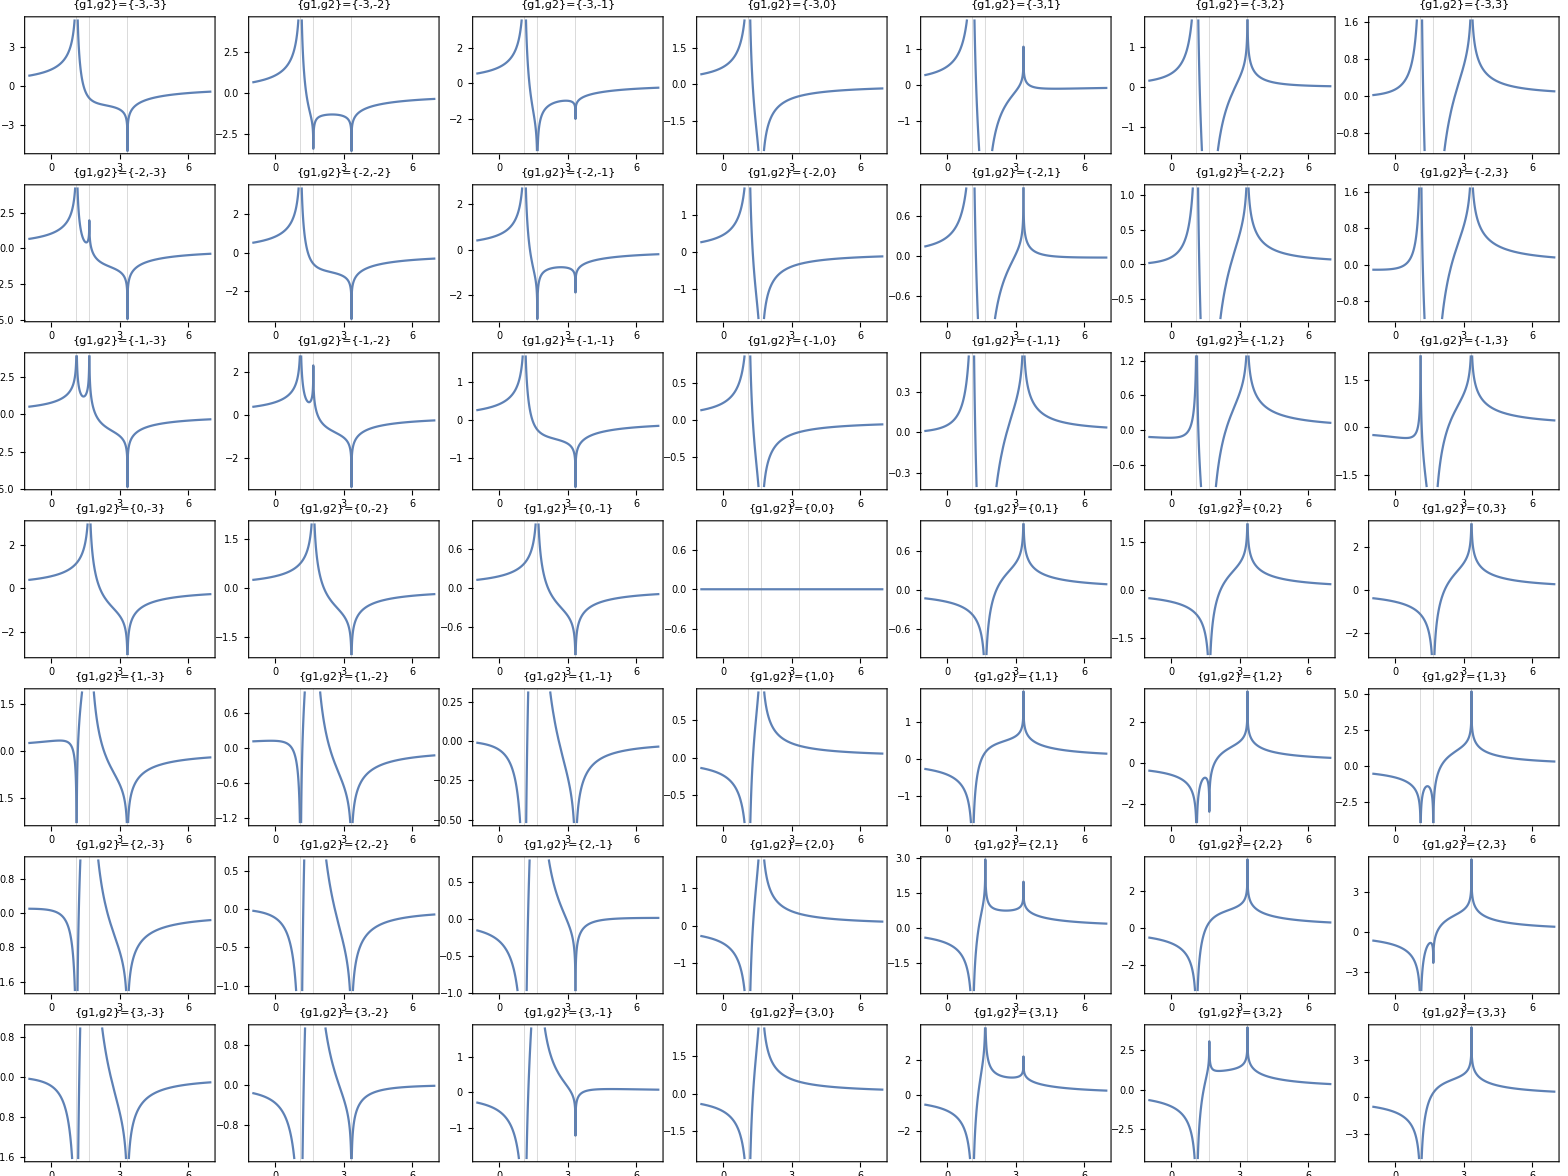

```mathematica
diffg1g2Plt=Table[
Plot[
omegaFunMZAGeneral[n,0.9,0.3,0.6,g1,g2],
{n,-1,7},Frame->True,ImageSize->Small,GridLines->{{1/0.3,1/0.6,1/0.9}, None},PlotLabel->"{g1,g2}={"<>ToString@g1<>","<>ToString@g2<>"}"],
{g1,-3,3,1},{g2,-3,3,1}]//Grid
```

```mathematica
Export["export/diffg1g2Plt.png",diffg1g2Plt]
```

export/diffg1g2Plt.png

```mathematica
Assuming[a∈Reals&&b∈Reals,
Integrate[1/x,{x,a,b}]
]
```

ConditionalExpression[Log[b/a],0<a<b]

```mathematica
a
```